# N-atom with randomized spacing

## Generating the tansfer matrix

### Transfer matrix of a cell

```mathematica
ClearAll;
```

```mathematica
M [k_,Γ_,Ω_,L_]:= {{ Exp[I k L](1-ⅈ Γ/(Ω-k)),-I Exp[-I k L] (Γ/(Ω-k))},{I Exp[I k L](Γ/(Ω-k)),Exp[-I k L] (1+ⅈ Γ/(Ω-k))}}
```

### Generating Normal Variate

```mathematica
GenerateNormalVariate[NoVar_,mean_,var_]:=Module[{ctr,NewNo,tmp1,tmp2,tmp3},NewNo=If[EvenQ[NoVar],NoVar,NoVar+1];
tmp1=Table[RandomReal[],{ctr,1,NewNo}];
tmp2=Table[{Sqrt[-2 Log[tmp1[[2 ctr-1]]]] Cos[2 Pi tmp1[[2 ctr]]] Sqrt[var]+mean,Sqrt[-2 Log[tmp1[[2 ctr-1]]]] Sin[2 Pi tmp1[[2 ctr]]] Sqrt[var]+mean},{ctr,1,NewNo/2}];
tmp3=Table[Flatten[tmp2][[ctr]],{ctr,1,NoVar}];
Return[tmp3];]
```

### Putting it all together

```mathematica
μ=Pi; σ=0.1;(*Mean periodicity(c/Ω), standard deviation *)
```

```mathematica
Subscript[M, system][k_,Γ_,Ω_,N1_,M_]:=Module[{matrix,temp,l},
l= GenerateNormalVariate[N1,μ,σ];
(* Random Spacing Generator, in terms of Subscript[λ, r]*)
matrix=Table[M[k,Γ,Ω,l[[j]]],{j,1,N1}];
temp=Fold[Times,1,matrix];
Return[temp];]
```

```mathematica
t[k_,Γ_,Ω_,N1_,M_,P_]:= 1/Abs[P[k,Γ,Ω,N1,M][[2,2]]]
```

## Anderson Localisation

```mathematica
(*Declaring global variable*)
N1=100;(*Number of atoms*)
Ω = 1;Γ = 1;
```

```mathematica
λ[k_]:=Log[E,
Abs[Eigenvalues[Subscript[M, system][k,Γ,Ω,N1,M]][[1]]]
]^-1
```

```mathematica
Clear[lambdaMatrix]
```

```mathematica
lambdaMatrix[NoRuns_,lowerfreq_,upperfreq_]:=Module[{tmp,incr},tmp={};
incr = (upperfreq-lowerfreq)/NoRuns;
For[k=lowerfreq,k≤ upperfreq,k+=incr,AppendTo[tmp,{k,λ[k]}]];
Return[tmp]
]
```

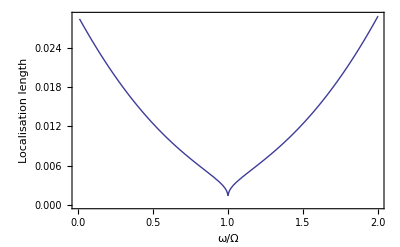

```mathematica
ListLinePlot[lambdaMatrix[1000,0.01,2],
FrameLabel->{"ω/Ω","Localisation length"},
Frame->True]
```

```mathematica
(*Generate data sets and take the average*)
(*FWHM,Γ,N1 -> Bandgap*)
(*if R==1, then store frequency in list. Take difference between max and min frequency.store in FWM*)
```